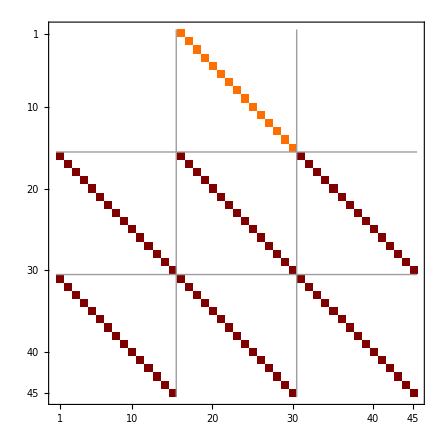

```mathematica
n=15;
q1=Array[Subscript[ρ, #]&,n,0];
q2=Array[Subscript[ρu, #]&,n,0];
q3=Array[Subscript[ρi, #]&,n,0];

F1=Array[Subscript[ρu, #]&,n,0];
F2=Array[Subscript[ρu, #]^2/Subscript[ρ, #]+P[Subscript[ρ, #],Subscript[ρi, #]]&,n,0];
F3=Array[Subscript[ρu, #]/Subscript[ρ, #](Subscript[ρi, #]+P[Subscript[ρ, #],Subscript[ρi, #]])&,n,0];

q=Join[q1,q2,q3];
F=Join[F1,F2,F3];

J = SparseArray[D[F, {q}]];
MatrixPlot[J,Mesh-> {2,2}]
```

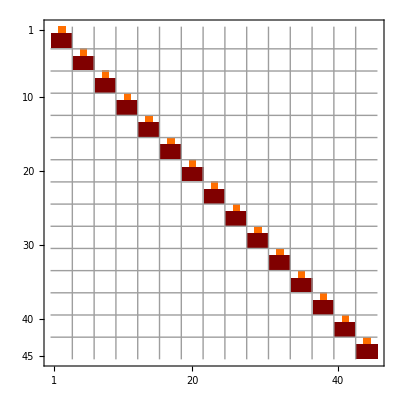

```mathematica
q = Riffle[Riffle[q1,q2],q3,{3,3n,3}];
F = Riffle[Riffle[F1,F2],F3,{3,3n,3}];
J = D[F, {q}];
MatrixPlot[J,Mesh-> {n-1,n-1}]
```

```mathematica
D[p2((x - μ1)/μ2)^2+p1((x - μ1)/μ2)^1+p0((x - μ1)/μ2)^0,{x,1}]
```

(2 p2 (x-μ1))/μ2^2+p1/μ2